```mathematica
SetDirectory[NotebookDirectory[]];
```

## Individual runs for Slides

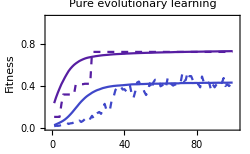

```mathematica
c0bi =Flatten[ Import["c0_b_i.dat","CSV"]];
c0ai = Flatten[ Import["c0_a_i.dat","CSV"]];
c0bm =Flatten[  Import["c0_b_m.dat","CSV"]];
c0am =Flatten[  Import["c0_a_m.dat","CSV"]];
ListLinePlot[{c0bi,c0ai,c0bm,c0am},PlotRange->{{-2,102},{0.0,1.05}},Frame->True,FrameLabel->{"Lifetime and evolutionary learning events","Fitness"},ImageSize->250,PlotStyle->{Directive[Dashed,ColorData["Rainbow"][0.05]],Directive[Dashed,ColorData["Rainbow"][0.15]],Directive[Dashing[None],ColorData["Rainbow"][0.05]],Directive[Dashing[None],ColorData["Rainbow"][0.15]]},PlotLabel->"Pure evolutionary learning"]
Export["slides_0.png",%];
```

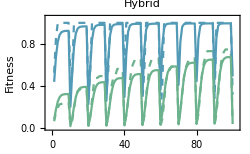

```mathematica
c0bi =Flatten[ Import["c3_b_i.dat","CSV"]];
c0ai = Flatten[ Import["c3_a_i.dat","CSV"]];
c0bm =Flatten[  Import["c3_b_m.dat","CSV"]];
c0am =Flatten[  Import["c3_a_m.dat","CSV"]];
ListLinePlot[{c0bi,c0ai,c0bm,c0am},PlotRange->{{-2,102},{0.0,1.05}},Frame->True,FrameLabel->{"Lifetime and evolutionary learning events","Fitness"},ImageSize->250,PlotStyle->{Directive[Dashed,ColorData["Rainbow"][0.33]],Directive[Dashed,ColorData["Rainbow"][0.43]],Directive[Dashing[None],ColorData["Rainbow"][0.33]],Directive[Dashing[None],ColorData["Rainbow"][0.43]]},PlotLabel->"Hybrid"]
Export["slides_3.png",%];
```

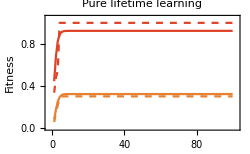

```mathematica
c0bi =Flatten[ Import["c6_b_i.dat","CSV"]];
c0ai = Flatten[ Import["c6_a_i.dat","CSV"]];
c0bm =Flatten[  Import["c6_b_m.dat","CSV"]];
c0am =Flatten[  Import["c6_a_m.dat","CSV"]];
ListLinePlot[{c0bi,c0ai,c0bm,c0am},PlotRange->{{-2,102},{0.0,1.05}},Frame->True,FrameLabel->{"Lifetime and evolutionary learning events","Fitness"},ImageSize->250,PlotStyle->{Directive[Dashed,ColorData["Rainbow"][0.95]],Directive[Dashed,ColorData["Rainbow"][0.85]],Directive[Dashing[None],ColorData["Rainbow"][0.95]],Directive[Dashing[None],ColorData["Rainbow"][0.85]]},PlotLabel->"Pure lifetime learning"]
Export["slides_6.png",%];
```

## Steepest

```mathematica
sn = Import["steepest_nonlamarck_conditions.dat","CSV"];
```

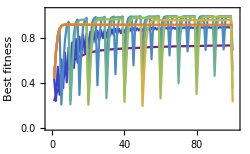

```mathematica
ListLinePlot[sn,PlotRange->{{-2,102},{0.0,1.05}},Frame->True,FrameLabel->{"Lifetime and evolutionary learning events","Best fitness"},ImageSize->250,PlotStyle->Table[ColorData["Rainbow"][x],{x,0,1,1/7}](*,PlotLabel->"Non-Lamarckian (K=6)"*)]
Export["steepest_nonlamarck_k6.eps",%];
```

```mathematica
sn = Import["5000_steepest_nonlamarck.dat","CSV"];
```

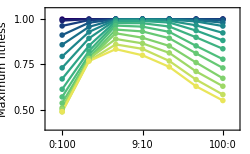

```mathematica
ListLinePlot[sn,PlotMarkers->●,PlotRange->{{0.5,7.5},{0.4,1.05}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["steepest_nonlamarck.eps",%];
```

```mathematica
sl = Import["steepest_lamarck_conditions.dat","CSV"];
```

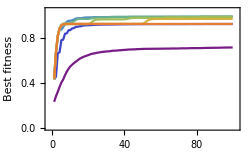

```mathematica
ListLinePlot[sl,PlotRange->{{-2,102},{0.0,1.05}},Frame->True,FrameLabel->{"Lifetime and evolutionary learning events","Best fitness"},ImageSize->250,PlotStyle->Table[ColorData["Rainbow"][x],{x,0,1,1/7}](*,PlotLabel->"Non-Lamarckian (K=6)"*)]
Export["steepest_lamarck_k6.eps",%];
```

```mathematica
sl= Import["5000_steepest_lamarck.dat","CSV"];
```

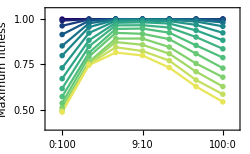

```mathematica
ListLinePlot[sl,PlotMarkers->●,PlotRange->{{0.5,7.5},{0.4,1.05}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["steepest_lamarck.eps",%];
```

```mathematica
sd=sl-sn;
```

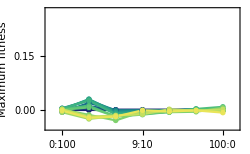

```mathematica
ListLinePlot[sd,PlotMarkers->●,PlotRange->{{0.5,7.5},{-0.05,0.28}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["diff_inheritance.eps",%];
```

## Stochastic

```mathematica
cn= Import["5000_stochastic_nonlamarck.dat","CSV"];
```

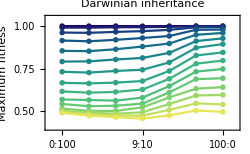

```mathematica
ListLinePlot[cn,PlotMarkers->●,PlotRange->{{0.5,7.5},{0.4,1.05}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotLabel->"Darwinian inheritance",PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["stochastic_nonlamarck.eps",%];
```

```mathematica
cl= Import["5000_stochastic_lamarck.dat","CSV"];
```

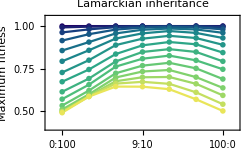

```mathematica
ListLinePlot[cl,PlotMarkers->●,PlotRange->{{0.5,7.5},{0.4,1.05}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotLabel->"Lamarckian inheritance",PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["stochastic_lamarck.eps",%];
```

```mathematica
cd=cl-cn;
```

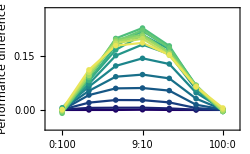

```mathematica
ListLinePlot[cd,PlotMarkers->●,PlotRange->{{0.5,7.5},{-0.05,0.28}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Performance difference"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["stochastic_diff_inheritance.eps",%];
```

```mathematica
x=sn-cn;
```

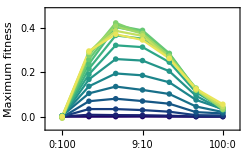

```mathematica
ListLinePlot[x,PlotMarkers->●,PlotRange->{{0.5,7.5},{-0.05,0.48}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["diff_inheritance.eps",%];
```

```mathematica
x=sl-cl;
```

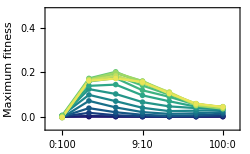

```mathematica
ListLinePlot[x,PlotMarkers->●,PlotRange->{{0.5,7.5},{-0.05,0.48}},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotStyle->Table[ColorData["BlueGreenYellow"][x],{x,0,1,1/14}]]
Export["diff_inheritance.eps",%];
```

## Diff Steep

```mathematica
dsl= Import["5000_diffsteep_lamarck.dat","CSV"];
```

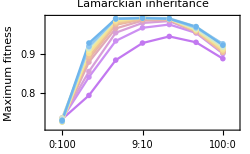

```mathematica
ListLinePlot[dsl,PlotMarkers->●,PlotRange->{{0.5,7.5},Automatic},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotLabel->"Lamarckian inheritance",PlotStyle->Table[ColorData["Pastel"][x],{x,0,1,1/14}]]
Export["5000_diffsteep_lamarck.eps",%];
```

```mathematica
dsd= Import["5000_diffsteep_nonlamarck.dat","CSV"];
```

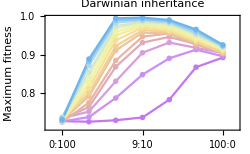

```mathematica
ListLinePlot[dsd,PlotMarkers->●,PlotRange->{{0.5,7.5},Automatic},Frame->True,FrameTicks->{{Automatic,None},{{{1,"0:100"},{2,"1:50"},{3,"4:20"},{4,"9:10"},{5,"19:5"},{6,"49:2"},{7,"100:0"}},None}},FrameLabel->{"Lifetime and evolutionary learning events (L:E)","Maximum fitness"},ImageSize->250,PlotLabel->"Darwinian inheritance",PlotStyle->Table[ColorData["Pastel"][x],{x,0,1,1/14}]]
Export["5000_diffsteep_darwin.eps",%];
```